# Problem Set 5

## Problem 3

## a)

```mathematica
f[x_]:= ArcTan[x]
```

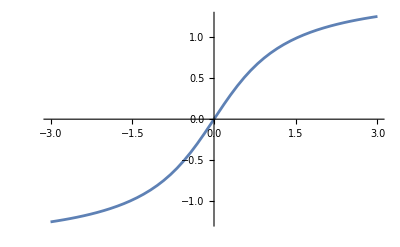

```mathematica
Plot[f[x],{x,-3,3}]
```

```mathematica
f'[x]
```

1/(1+x^2)

```mathematica
h = 0.2
```

0.2

```mathematica
R[h_]:=ArcTan[h]/h
```

```mathematica
R1[h_]:=1/3 *((4 ArcTan[h/2])/(h/2) - ArcTan[h]/h)
```

```mathematica
R2[h_]:=1/15 * (16 R1[h/2] - R1[h])
```

```mathematica
1/15(16/3((4 ArcTan[h/4])/(h/4) - ArcTan[h/2]/(h/2)) - 1/3((4 ArcTan[h/2])/(h/2) - ArcTan[h]/h))
```

1.

```mathematica
NumberForm[0.999999862780083,16]
```

0.999999862780083

```mathematica
R1[0.2]
```

0.999923

```mathematica
R2[0.2]
```

1.

```mathematica
NumberForm[0.999999862780083,16]
```

0.999999862780083

## b)

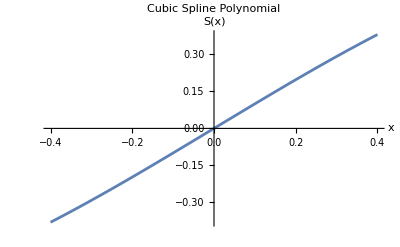

```mathematica
(*Define h and the function values at the points*)h=0.2;

(*Define the function f(x)=ArcTan(x)*)
f[x_]:=ArcTan[x]

(*Define the equations using f[-2h],f[-h],f[h],and f[2h]*)
eq1=f[-2 h]==a (-2 h)^3+b (-2 h)^2+c (-2 h)+d;
eq2=f[-h]==a (-h)^3+b (-h)^2+c (-h)+d;
eq3=f[h]==a (h)^3+b (h)^2+c (h)+d;
eq4=f[2 h]==a (2 h)^3+b (2 h)^2+c (2 h)+d;

(*Solve the system of equations*)
solution=Solve[{eq1,eq2,eq3,eq4},{a,b,c,d}];


(*Extract coefficients a,b,c,d*)
{a,b,c,d}={a,b,c,d}/. solution[[1]];

(*Construct the polynomial*)
polynomial[x_]:=a x^3+b x^2+c x+d;

(*Plot the polynomial over the range of interest*)
Plot[polynomial[x],{x,-2 h,2 h},PlotRange->All,AxesLabel->{"x","S(x)"},PlotLabel->"Cubic Spline Polynomial"]
```

```mathematica
solution
```

{{-0.297599→-0.297599,3.67389×10^-16→3.67389×10^-16,0.998882→0.998882,-5.87326×10^-17→-5.87326×10^-17}}